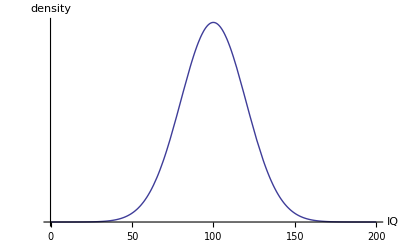

```mathematica
g1=Plot[PDF[NormalDistribution[100,20],IQ],{IQ,0,200},BaseStyle->{FontSize->16},AxesLabel->{"IQ ","density "},Ticks->{True,None},ImagePadding->{{30,100},{30,30}}]
```

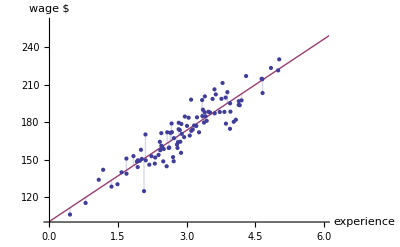

```mathematica
NN= 100;
experience=RandomVariate[NormalDistribution[3,1],{NN}];
error = RandomVariate[NormalDistribution[0,10],{NN}];
wage= Map[100 + 25 #& , experience]+error;
data = Thread[{experience,wage}];
lm=LinearModelFit[data,x,x];
g2=ListPlot[{data,Table[{x,lm[x]},{x,0,7}]},Joined->{False,True},Filling->1->{2},PlotRange->{{0,6},{100,260}},AxesLabel->{"experience ","wage $ "},BaseStyle->{FontSize->16},ImagePadding->{{30,100},{30,30}}]
```

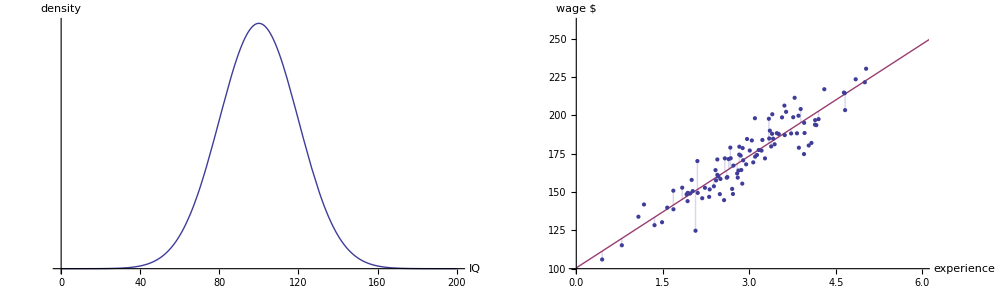

```mathematica
Show[GraphicsRow[{g1,g2}],ImageSize->1000]
```